```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-12-20"}];

dropBoxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns"}];
If[SystemInformation["Kernel","OperatingSystem"]=="Unix",
folder=FileNameJoin[{"/","home","karl",dropBoxOn}]; ,(* Home coputer is Linux, so needs "/" at beginning *)
folder=FileNameJoin[{"C:","Users","kahrendsen2",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"*)
];
SetDirectory[folder];

FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-05-25_LaserProfiling - Shortcut.lnk,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_exFnCurrentNormalized.png,18-01-28_exFnMolyCounts.png,18-01-28_exFnRawCounts.png,18-01-28_exFnSignalCounts.png,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-24_DataFrom18-02-13AllElectronEi100,18-02-27,18-03-01,18-03-02,18-03-03,18-03-06_RubidiumOnWalls,18-03-18_100mTorrBGP,18-03-22_Ei=37eV,18-03-23_pumpScan,18-03-24_higherTemps350mTorr,18-03-25_springBreakDataReview,18-03-27_770mTorr,18-03-28_PumpPowerScan,18-04-09_PumpLaserRazorProfile,dataDump,POL2018-03-18.dat,pumpQWP,reallyNiceData,temp,test.png,wavemeterOffsets}

```mathematica
(* set rootFolder to the folder name containing the desired Files *)
rootFolder=FileNameJoin[{folder,"18-03-22_Ei=37eV","data"}];
SetDirectory[rootFolder];
(* Obtain the filenames of the rotation data and print them out.*)
absFiles=FileNames["RbAbs"~~RegularExpression[".{17,17}"]~~".dat"];
absFiles
```

{RbAbs2018-03-21_171118.dat,RbAbs2018-03-21_184907.dat,RbAbs2018-03-21_201044.dat,RbAbs2018-03-21_214830.dat,RbAbs2018-03-21_231006.dat,RbAbs2018-03-22_004748.dat,RbAbs2018-03-22_020918.dat,RbAbs2018-03-22_034703.dat,RbAbs2018-03-22_050908.dat,RbAbs2018-03-22_064650.dat,RbAbs2018-03-22_080851.dat,RbAbs2018-03-22_094633.dat,RbAbs2018-03-22_110822.dat,RbAbs2018-03-22_124604.dat,RbAbs2018-03-23_001504.dat,RbAbs2018-03-23_012104.dat,RbAbs2018-03-23_015019.dat,RbAbs2018-03-23_025617.dat,RbAbs2018-03-23_032530.dat,RbAbs2018-03-23_043128.dat,RbAbs2018-03-23_050040.dat,RbAbs2018-03-23_060639.dat,RbAbs2018-03-23_063552.dat,RbAbs2018-03-23_074159.dat,RbAbs2018-03-23_081113.dat,RbAbs2018-03-23_091722.dat,RbAbs2018-03-23_094634.dat,RbAbs2018-03-23_105239.dat,RbAbs2018-03-23_112153.dat,RbAbs2018-03-23_122758.dat,RbAbs2018-03-23_125712.dat,RbAbs2018-03-23_140315.dat,RbAbs2018-03-23_143225.dat,RbAbs2018-03-23_153828.dat,RbAbs2018-03-23_160738.dat,RbAbs2018-03-23_171348.dat,RbAbs2018-03-23_205558.dat,RbAbs2018-03-23_221056.dat,RbAbs2018-03-23_233148.dat,RbAbs2018-03-24_004651.dat,RbAbs2018-03-24_020802.dat,RbAbs2018-03-24_032259.dat,RbAbs2018-03-24_044419.dat,RbAbs2018-03-24_055906.dat,RbAbs2018-03-24_072018.dat,RbAbs2018-03-24_083508.dat,RbAbs2018-03-24_095636.dat,RbAbs2018-03-24_111124.dat}

```mathematica
FixBrokenWavemeterValues[dat_]:=Module[{},dat[Select[#WAV>7000000&]]]
```

<|Filename→/home/pi/RbData/2018-03-21/RbAbs2018-03-21_214830.dat,Comments→temp=106, E_i=37.3 eV, tried 2 eV but the current was too low., prelude,IonGauge(Torr)→0.000168,CVGauge(N2)(Torr)→0.126,CVGauge(He)(Torr)→0.00117,CurrTemp(Res)→106.,SetTemp(Res)→106.,CurrTemp(Targ)→150.,SetTemp(Targ)→150.|>

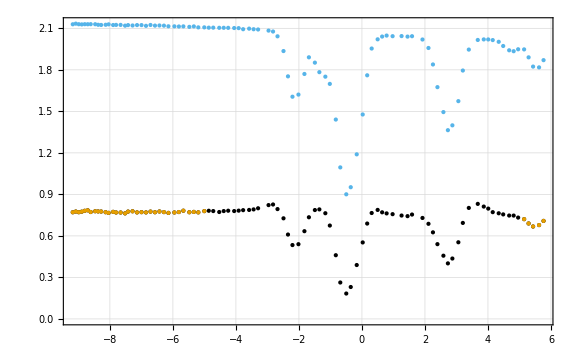

```mathematica
index=4;
GetIndexOfFilenameFromTimestamp[absFiles,"171118"];
head=GetFileHeaderInfo[absFiles[[index]]]
dat=GetFileDataset[absFiles[[index]]];
maxIntensity=3.4789;
minIntensity=.015;
validEntries=FixBrokenWavemeterValues[dat];(* Selects all of the data that isn't missing *)

detAdded=validEntries[All,<|#,"DETUNING"->c/100/(#WAV/10000)-ν0,"PRBminRemoved"->#PRB-minIntensity|>&];

detAdded=detAdded[All,<|#,"PRBnorm"->#PRBminRemoved/maxIntensity|>&];
wingsData=detAdded[Select[Abs[#["DETUNING"]]>5&]];
wingsData[All,{"DETUNING","PRB"}];
wingsLinearModel=LinearModelFit[Normal[wingsData[All,{"DETUNING","PRBnorm"}][Values]],x,x];
ListPlot[{detAdded[All,{"DETUNING","PRBnorm"}],wingsData[All,{"DETUNING","PRBnorm"}],detAdded[All,{"DETUNING","REF"}][Values]}]
```

65.4

64.5

0

125

150

{{-7.64405,0.238088},{-8.18163,0.237102},{-8.75084,0.234082},{-9.27261,0.226892},{-9.84182,0.23072},{-10.391,0.229802},{-10.9912,0.223731},{-11.502,0.222272},{-12.2135,0.221349},{-12.8301,0.224263},{-13.4467,0.219068},{-14.1108,0.21988},{-14.7274,0.216229},{-15.344,0.218899},{-16.0555,0.220595},{-31.5652,0.206994},{-33.0829,0.206008},{-34.0789,0.206364},{-34.98,0.208545},{-35.8811,0.206511}}

0

{{27.5871,0.213865},{27.1601,0.210853},{26.828,0.213719},{26.3536,0.214602},{25.8317,0.210917},{12.311,0.225979},{11.3148,0.226027},{10.5558,0.224188},{9.79675,0.225812},{8.94286,0.231502},{8.27872,0.23508},{7.51971,0.23826},{6.7607,0.25195},{6.0017,0.272224},{5.33757,0.401037},{4.62601,0.194585},{3.86702,0.328372},{3.10802,0.429306},{2.3016,0.189191},{1.59005,0.206502}}

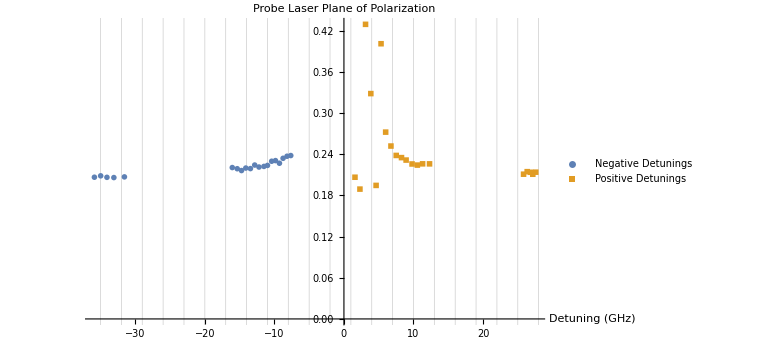

63.4682

0.240116

0.00378325

```mathematica
(* Define important constants of data processing *)
maxFileNumber=1;
minFileNumber=2;
dataFileNumber=3;

negFileNumber=13;
posFileNumber=16;
rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[maxFileNumber]]}],"tsv"];
rotAnalDataStartRow=16; (* Used to know how many lines to remove so we are just working with data *)
aoutColumn=1;
wavelengthColumn=2;
angleColumn=10;

(* Define important physical constants*)
c=2.99792458*^8;
ν0=377107.463;
(* Retrieves the recorded voltages of the magnets *)
v1=rotationAnalysisData[[11]][[2]]
v2=rotationAnalysisData[[12]][[2]]
(* The coefficients for the polynomial describing the magnetic field of magnet 1 [(c)oefficient of magent (1)]  based on the current.
Assumes x is measured in cm *)
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;

(* The coefficients for the linear relationship between the current and the voltage of the magnets *)
c1v2iSlope=.0504;
c1v2iInt=-.0113;
c2v2iSlope=.0488;
c2v2iInt=-.0069;

(* Calculate the current in each of the magnets based on the voltage *)
i1=v1*c1v2iSlope+c1v2iInt;
i2=v2*c2v2iSlope+c2v2iInt;

(*Creates a function for obtaining the magnetic field at a given position based on the currents
in the magnets *)
getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) x^2 +((c1x1 )i1 +(c2x1)i2) x +((c1x0 )i1 +(c2x0)i2)  ;
BdotL=Integrate[getBEq[i1,i2],{x,0,2.794}] /100/10000;(* Divide by 100 to convert to Gauss*meters, Divide by 10000 to convert to Tesla*meters*)



rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedFrequencies[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
negativeDetunings=ConvertFDayDegreeToRadian[ConvertFDayWavelengthToDetune[rotationAnalysisData]]

rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[posFileNumber]]}],"tsv"];
rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedFrequencies[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
positiveDetunings=ConvertFDayDegreeToRadian[ConvertFDayWavelengthToDetune[rotationAnalysisData]]


allDetuningsPlot=ListPlot[{Legended[negativeDetunings,"Negative Detunings"],Legended[positiveDetunings,"Positive Detunings"]},PlotRange->All,LabelStyle->18,PlotMarkers->{Automatic,Large},AxesLabel->{"Detuning (GHz)","Probe Laser\nPlane of Polarization"},ImageSize->Large,GridLines->{Range[-35,35,3],None}]

allDetunings=Join[negativeDetunings,positiveDetunings];
detMinMax={Min[Transpose[allDetunings][[1]]],Max[Transpose[allDetunings][[1]]]};
angleMinMax={Min[Transpose[allDetunings][[2]]],Max[Transpose[allDetunings][[2]]]};
run=detMinMax[[2]]-detMinMax[[1]]
rise=angleMinMax[[2]]-angleMinMax[[1]]
rise/run
```

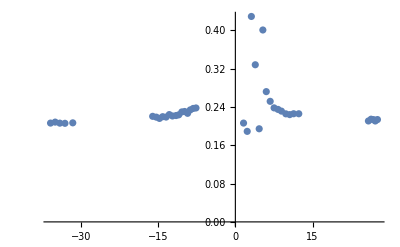

```mathematica
modelA4=a1/(δ)^2+a2/(δ)^4+θ0;
modelA2=a1/(δ)^2+θ0;
modelB4=a1/(δ-b)^2+a2/(δ-b)^4+θ0;
modelB2=a1/(δ-b)^2+θ0;


negativeCutoffs={8,40};
positiveCutoffs={8,40};
linearSlope=-.00;
detuningOffset=0;

positiveDetuningsZeroed=SubtractLinearSlope[positiveDetunings,linearSlope];

negativeDetuningsZeroed=SubtractLinearSlope[negativeDetunings,linearSlope];

allDataZeroed=Join[positiveDetuningsZeroed,negativeDetuningsZeroed];
ListPlot[allDataZeroed,PlotRange->Full]
```

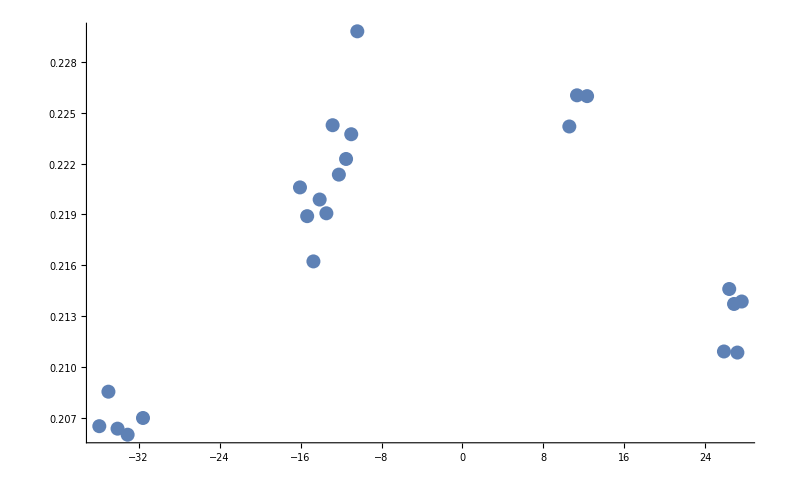

Fit Parameters for Number Density

{a1→5.12226,a2→-278.661,θ0→0.204084,b→1.82321}

Parameter Errors 1/δ^2+1/δ^4

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

Replacements Excluding δ^4

{a1→2.25359,θ0→0.207613,b→0.0494005}

Parameter Errors 1/δ^2

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{0.196612,0.000988959,0.308518}

Number Density (cm^-3):

3.17436×10^12

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

Number Density Error (cm^-3):

2.7603×10^11

Number Density Simple(cm^-3):

1.39659×10^12

Number Density Simple Error(cm^-3):

1.21844×10^11

-Graphics-

```mathematica
(* Calculates fit for data *)
(* Removes datapoints that wrapped in rotation *)
For[low=5,low<6,low+=5,
lowerBoundDetuning=10;
upperBoundDetuning= 40;
dataset=Dataset[allDataZeroed];
dataset=dataset[Select[Abs[#[[1]]]<upperBoundDetuning&]];
dataset=dataset[Select[Abs[#[[1]]]>lowerBoundDetuning&]];
Print[ListPlot[dataset]];
alldata = Normal[dataset];
labelSize=18;

ClearAll[δ,a1,a2,c,θ0,b,nlmFit,replacements];
$Assumptions=a1>0;
$Assumptions=a2>0;
dataset=Dataset[alldata];
min=dataset[Min,2];
max=dataset[Max,2];
maxmin={max,min};
ListPlot[Normal[dataset],PlotRange->All];
νo=377.107;
Print["Fit Parameters for Number Density"];
nlmFit =NonlinearModelFit[Normal[dataset],{modelB4,a1>0},{{a1,1},{a2,1},{θ0,0},{b,1}},δ];
replacements=nlmFit["BestFitParameters"];
Print[replacements];
plot=Plot[Legended[Evaluate[modelB4/.replacements],"A_1/(δ - B)^2+A_2/(δ - B)^4+θ_o"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->color,LabelStyle->labelSize];
Print["Parameter Errors 1/δ^2+1/δ^4"];
errors=nlmFit["ParameterErrors"];
{δl,θl}=Transpose[Normal[dataset]];


Print["Replacements Excluding δ^4"];
nlmFit2=NonlinearModelFit[Normal[dataset],{modelB2,a1>0},{{a1,4},{θ0,0},{b,1}},δ,AccuracyGoal->5];
replacementsNo4=nlmFit2["BestFitParameters"];
Print[replacementsNo4];
plotNo4=Plot[Legended[Evaluate[modelB2/.replacementsNo4],"A_1/(δ - B)^2+θ_o"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->Red,LabelStyle->labelSize];
modelfNo4=Function[{δ},Evaluate[modelB2/.replacementsNo4]];
{δl,θl}=Transpose[Normal[dataset]];
Print["Parameter Errors 1/δ^2"];
errorsNo4=nlmFit2["ParameterErrors"];
Print[errorsNo4];

linearRotationFit=LinearModelFit[Normal[dataset],x,x];

c=2.99792458*^8;
re=2.8179*^-15;
fge=0.34231;
k=4/3;
BdotL;
μ=9.2740*^-24;
h=6.6261*^-34;
ν0=377107.463;
conversionFactor=h/(BdotL*c*re*fge*k*μ)*10^18*10^-6;(*Conversion Factor is in 1/(Hz)^2, so we need *10^18 to convert to 1/(GHz)^2*)

Print["Number Density (cm^-3):"];
n=(a1/.replacements)* conversionFactor;
Print[n];
errors=nlmFit["ParameterErrors"];
Print["Number Density Error (cm^-3):"];
nErr=errors[[1]]*conversionFactor;
Print[nErr];

Print["Number Density Simple(cm^-3):"];
nNo4 =(a1/.replacementsNo4)*conversionFactor;
Print[nNo4];
Print["Number Density Simple Error(cm^-3):"];
nErr=errorsNo4[[1]]*conversionFactor;
Print[nErr];

finalResult=Show[plot,plotNo4,ListPlot[Legended[Normal[dataset],"Data Points"],LabelStyle->labelSize],Epilog->Inset[Style["2.0(3)×10^12cm^-3",14],{20,.025}],AxesLabel->{"Detuning\n(GHz)","Plane of Polarization (rad)"},ImageSize->Large,PlotRange->All];

Print[Rasterize[finalResult]];
fitList={{"theta_0","A_1","B","theta_0'","A_1'","B'","A_2'"},
{θ0/.replacementsNo4,a1/.replacementsNo4,b/.replacementsNo4,θ0/.replacements,a1/.replacements,b/.replacements,a1/.replacements},
{errorsNo4[[2]],errorsNo4[[1]],errorsNo4[[3]],errors[[3]],errors[[1]],errors[[4]],errors[[2]]}};
Export["fitStatistics_DetuningCutoff"<>ToString[low]<>".tsv",fitList];
Export["fitGraph_DetuningCutoff"<>ToString[low]<>".png",finalResult];
]
```

```mathematica
ConvertAoutToDetuneUsingTransitions[fileName_,trans1_,letterFirst_,letterLast_]:=Module[{CtoDDiff,BtoCDiff,AtoBDiff,dt,ct,bt,at,transGHz,aoutSteps,s,startPos,scanStepSize,posLower,posUpper,transAout,i,j,k,peak,aoutPos,aoutPrev,aoutNextApprox,aoutConvData,lm,aoutConv,aoutIntercept,rbAbsorptionRefT,rbAbsorptionRefDet,transitionLines, rbAbsorptionProT,rbAbsorptionProDet},
CtoDDiff=110;
BtoCDiff=125;
AtoBDiff=72;
dt=4.576;
ct=1.84;
bt=-1.372;
at=-3.072;
transGHz={4.576,1.84,-1.372,-3.072};
aoutSteps={CtoDDiff,BtoCDiff,AtoBDiff};

(*Find the closest data point to the value chosen by the user*)
s=Nearest[Take[rbAbsorptionRef,All,1],trans1];
(*Convert this data point to a position in the list*)

startPos=Position[Take[rbAbsorptionRef,All,1],s[[1]]][[1]][[1]];
(*Use the position in the list to find the first absorption peak's value*)
scanStepSize=Abs[(rbAbsorptionRef[[startPos]]-rbAbsorptionRef[[startPos+1]])[[1]]];
posLower=startPos-3;
posUpper=startPos+2;
transAout={0,0,0,0};
i=0;

If[letterFirst=="D",j=1,If[letterFirst=="C",j=2,If[letterFirst=="B",j=3,If[letterFirst=="A",j=4,j=5]]]];
If[letterLast=="D",k=1,If[letterLast=="C",k=2,If[letterLast=="B",k=3,If[letterLast=="A",k=4,k=5]]]];
(*Cycle through and find the remaining transisition "peaks"*)
While[And[j≤k],
peak=Min[Take[rbAbsorptionRef,{posLower,posUpper},All]];
(*Use the value of the first absorption peak to find its position in the list*)
aoutPos=Position[rbAbsorptionRef,peak][[1,1]];
(*Use the position in the list to get the Aout value located there*)
transAout[[j]]=rbAbsorptionRef[[aoutPos,1]];
(*Because the profile is consistent,we can guess at where the next min.will be*)
If[j<4,aoutPrev=transAout[[j]];aoutStep=aoutSteps[[j]];
aoutNextApprox=aoutPrev+aoutStep;
s=Nearest[Take[rbAbsorptionRef,All,1],aoutNextApprox];
posLower=aoutPos+Floor[aoutStep/scanStepSize]-2*Floor[10/scanStepSize];
posUpper=aoutPos+Floor[aoutStep/scanStepSize]+2*Floor[10/scanStepSize];];
j++;];

(*Remove the transistions that we don't have from the list so that we can estimate a linear function relating the data points that we do have*)
aoutConvData=Dataset[Transpose[{transAout,transGHz}]];
aoutConvData=aoutConvData[Select[Abs[#[[1]]]>0&]]
aoutConvData=Normal[aoutConvData];


(*Make a linear fit on the data to obtain an AOUT->GHz Conversion*)
lm=LinearModelFit[aoutConvData,x,x];
aoutConv=lm["BestFitParameters"][[2]];
aoutIntercept=lm["BestFitParameters"][[1]];
rbAbsorptionRefT=Transpose[rbAbsorptionRef];
rbAbsorptionRefDet=Transpose[{rbAbsorptionRefT[[1]]*aoutConv +aoutIntercept,rbAbsorptionRefT[[2]]}];
transitionLines=Line[{{{transGHz[[1]],0},{transGHz[[1]],1}},{{transGHz[[2]],0},{transGHz[[2]],1}},{{transGHz[[3]],0},{transGHz[[3]],1}},{{transGHz[[4]],0},{transGHz[[4]],1}}}];
ListPlot[rbAbsorptionRefDet,PlotRange->{{-7,7},All},ImageSize->Large,
PlotLabel->"Reference Cell Profile",AxesLabel->{"Detuning (GHz)","Intensity (a.u.)"},AxesOrigin->{-6,0},Joined->True,LabelStyle->labelSize,Epilog->Style[transitionLines,Dotted]]

rbAbsorptionProT=Transpose[rbAbsorptionPro];
rbAbsorptionProDet=Transpose[{rbAbsorptionProT[[1]]*aoutConv +aoutIntercept,rbAbsorptionProT[[2]]}];
ListPlot[rbAbsorptionProDet,PlotRange->{{-7,7},All},PlotLabel-> "Target Cell Profile (N_2=1 mTorr)",AxesLabel->{"Detuning (GHz)","Intensity (a.u.)"},AxesOrigin->{-6,0},Joined->True,
LabelStyle->labelSize,Epilog->Style[transitionLines,Dotted]]
]

StripAbsorptionData[fileName_,desiredColumn_]:=Module[{rbAbsorption},
(*Import the absorption data*)
rbAbsorption=Import[FileNameJoin[{Directory[],fileName}],"tsv"];
Take[rbAbsorption,{1,10},All]
(* Drop the information from the file that isn't needed *)
rbAbsorptionRef=Drop[Take[rbAbsorption,{13,-2},{1,7}],None,{2,6}];
rbAbsorptionPro=Drop[Take[rbAbsorption,{13,-2},{1,5}],None,{2,4}];
(* Plot the data so the user can see the first minimum *)
ListPlot[{rbAbsorptionPro,rbAbsorptionRef},Ticks-> {Range[0,1023,20],Automatic},GridLines->{Range[0,1023,20],None}]
]

(* This is called on a dataset to fill in all of the missing frequency gaps.*)
FillInMissedFrequencies[rawdata_,columnMissing_,columnReference_]:=Module[{referenceSpacing,missingEntries,validEntries,adjacentSpots,estimatedFrequency,linearModel,dataCopy,dataReturn,position,approxValue,data2,k},
dataCopy=Dataset[rawdata];
dataReturn=Normal[dataCopy];
missingEntries=dataCopy[Select[#[[columnMissing]]<7000000&]];
missingEntries=Transpose[Normal[missingEntries]][[columnReference]];
For[k=1,k<=Length[missingEntries],k++,
approxValue=ApproximateFrequency[dataCopy,columnMissing,columnReference,missingEntries[[k]]];
(* Find the index of the missing value in the list *)
position=Position[dataCopy,missingEntries[[k]]][[1,1]];
(* Use the index to insert the approximate value in the data  *)
dataReturn[[position,columnMissing]]=approxValue;
];
dataReturn
];

(* This removes the majority of the data that we're not interested in for Faraday rotation purposes*)
StripFaradayData[data_]:=Drop[Take[data,{rotAnalDataStartRow,-1},{aoutColumn,angleColumn}],None,{wavelengthColumn+1,angleColumn-wavelengthColumn+1}];

(* Converts the wavelength value reported as an integer to a detuning (GHz) *)
ConvertFDayWavelengthToDetune[data_]:=Module[{wavelengthInteger,θ,lists,wavelengthnm,wavelength,detuning},
lists=Transpose[data];
wavelengthInteger=lists[[1]];
θ=lists[[2]];
wavelengthnm=wavelengthInteger/10000;
detuning=c/(wavelengthnm)-ν0;
Transpose[{detuning,θ}]
];

(* Converts the angle of rotation variable reported as a degree to radians.*)
ConvertFDayDegreeToRadian[data_]:=Module[{wavelengthInteger,θ,lists,wavelengthnm,wavelength,detuning,radian},
lists=Transpose[data];
wavelengthInteger=lists[[1]];
θ=lists[[2]];
radian=θ*Pi/180;
Transpose[{wavelengthInteger,radian}]
];

GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];

SubtractLinearSlope[data_,linearSlope_]:=Module[{detuning,angle,dataTranspose},
dataTranspose=Transpose[data];
detuning=dataTranspose[[1]];
angle=dataTranspose[[2]];
angle=angle-linearSlope*detuning;
Transpose[{detuning,angle}]
];
ZeroDataWithAsymptote[data_,nearResonanceCut_,largeDetuningCut_]:=Module[{model, dataset,nlmFit,replacements,temp,a1x,a2x,bx,θ0x,δx},
dataset=Dataset[data];
dataset=dataset[Select[Abs[#[[1]]]<largeDetuningCut&]];
dataset=dataset[Select[Abs[#[[1]]]>nearResonanceCut&]];

model=a1x/(δx)^2+a2x/(δx)^4+θ0x;
nlmFit =NonlinearModelFit[Normal[dataset],model,{{a1x,1},{a2x,1},{θ0x,0}},δx];
replacements=nlmFit["BestFitParameters"];

dataset =Transpose[Normal[data]];
dataset[[2]]=dataset[[2]]-θ0x/.replacements;
Transpose[{dataset[[1]],dataset[[2]]}]
];

(* I love these things. By creating a function with a module you can create "functions" in the traditional C programming sense, where you have multiple inputs with one output. *)
(* ApproximateFrequency calculates the approximate frequency in the missing gap of the frequency measurements that we collected. *)
ApproximateFrequency[data_,columnMissing_,columnReference_,missingEntry_]:=Module[{j,adjacentSpots,referenceSpacing,validEntries,fit}(*These are your local variables that aren't stored beyond the scope of the module.*),
(*Selects the data that is certainly an appropriate measure of wavelength *)
validEntries=Take[data,All,{1,2}];
validEntries=validEntries[Select[#[[columnMissing]]>7000000&]];
(*The "reference column" is the column that is monotonically increasing, we need to know what the size of spaces between these values is *)
referenceSpacing=Abs[data[[2]][[columnReference]]-data[[1]][[columnReference]]];
j=1;
(* This "While" loop accumulates adjacent data points used to approximate the missing frequency, we only want the closest datapoints. *)
While[And[Length[adjacentSpots]<3,Abs[j*referenceSpacing]<1024](* We want a few data points to approximate where our point lies, keep going until we have at least 3*),
adjacentSpots=validEntries[Select[Abs[#[[columnReference]]-missingEntry]≤referenceSpacing*j&]];
j++;
];
fit=LinearModelFit[Normal[adjacentSpots],x,x];
Print[missingEntry];
fit[missingEntry] (* Last line is the "return" statement, all other lines need a semi-colon*)
];
```